# DOMAČA NALOGA _1

## 1. Reši neenačbo:

```mathematica
Reduce[3x-2 ≤ 5x+4 ≤ x+6, x]
```

-3≤x≤1/2

```mathematica
Reduce[3x-4<2x+5≤ 6x+8,x]
```

-3/4≤x<9

```mathematica
Reduce[2x-3≤ 4x-5≤ -2x+1,x]
```

x==1

```mathematica
Reduce[(x-3)/4>x+3≥ (4+3x)/2,x]
```

x<-5

Ker je v zadnji rešitvi x manjši od 5, je zaradi tega tudi x manjši ali enak 2.

## 2. Dana je linearna funkcija 3 x - 10 y = 4. Določi njeno splošno enačbo, izračunaj začetno vrednost in ničlo ter zapiši odsekovno enačbo. Poišči še ploščino trikotnika, ki ga graf te funkcije omejuje skupaj s koordinatnima osema.

Splošna enačba linearne funkcije je y = 3/10 x-2/5

```mathematica
f[x_]:=3/10 x-2/5;
```

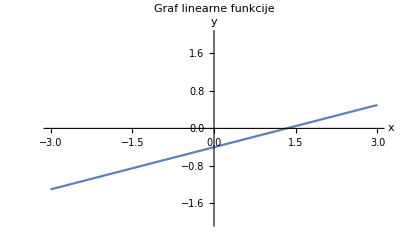

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{-2,2},AxesLabel->{"x","y"},PlotLabel->"Graf linearne funkcije"]
```

Da izračunamo začetno vrednost, funkciji vnesemo za x, f (0).

```mathematica
f[0]
```

-2/5

Da izračunamo ničle, enačbo enačimo z nič.

```mathematica
Solve[f[x]==0]
```

{{x→4/3}}

Odsekovna enačba:

```mathematica
x/(4/3)+y/(-2/5)=1;
```

Da pridobimo ploščino trikotnika, uporabimo pitagorov izrek, da pridobimo hipotenuza, in izrek o ploščini trikotnika s podanimi stranicami.

```mathematica
a=4/3;
b=-2/5;
c=√(a^2+b^2);
s=(a+b+c)/2;
FullSimplify[S=√(s(s-a)(s-b)(s-c))]
```

4/15

## 3. Racionaliziraj:

```mathematica
FullSimplify[(15 √2-6 √6)/(2 √6-3 √2)]
```

3+4 √3

```mathematica
FullSimplify[(56-2 √3)/(2 √6-√2)]
```

√2 (2+5 √3)

```mathematica
FullSimplify[(10 √5-4)/(4 √2+√10)]
```

√(58-24 √5)

```mathematica
FullSimplify[(1+18 √6)/(4 √2-√3)]
```

2 √2+5 √3

```mathematica
FullSimplify[(6-3 √2)/(3 √3-2 √6)]
```

√3 (2+√2)

```mathematica
FullSimplify[(3 √10)/(4 √5-5 √2)]
```

2 √2+√5

```mathematica
FullSimplify[(26 √2-8 √5)/(3 √5+√2)]
```

2 (-2+√10)

```mathematica
FullSimplify[(142+34 √5)/(3 √10+4 √2)]
```

√2 (-1+5 √5)

## 4. Uredi in reši kvadratno enačbo:

```mathematica
Solve [(3x-5)^2-(2x+3)*(2x-3)==2*(4x-7)]
```

{{x→8/5},{x→6}}

```mathematica
Solve[(2x+1)*(x-3)-(x-2)^2==2x+3]
```

{{x→-2},{x→5}}

```mathematica
Solve[(3x-2)^2-(2x-5)(2x+5)==2(2+9x)]
```

{{x→1},{x→5}}

```mathematica
Solve[(5x+1)^2-(4x-1)^2==(2x+1)^2+(2x+3)^2-7]
```

{{x→-3},{x→1}}

```mathematica
Solve[(3x-4)^2-(2x-3)(2x+3)==(5x+2)^2-28x]
```

{{x→-3/2},{x→7/10}}

## 5. Grafično in računsko poišči presečišče premice in parabole:

Da smo računsko odkrili presečišče premice in parabole, smo enačbi enačili. S tem smo odkrili presečišče na X osi. Da najdemo točke na Y osi, vnesemo odkrite točke v poljubno funkcijo. Z zadnjim korakom dobimo presečišče.

```mathematica
Solve[x^2-6x+5==x-1]
```

{{x→1},{x→6}}

```mathematica
Remove[f,x] (*Za vsak primer*)
```

```mathematica
f[x_]:=x-1;
```

```mathematica
f[1]
```

0

```mathematica
f[6]
```

5

P1(1,0), P2(6,5).

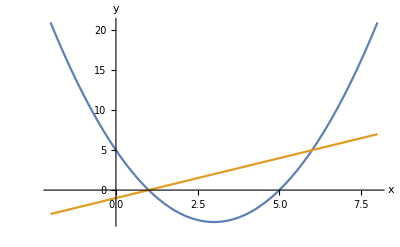

```mathematica
slika1=Plot[{x^2-6x+5,x-1},{x,-2,8}, AxesLabel->{"x","y"}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
Solve[x^2+8x+12==-x-2]
```

{{x→-7},{x→-2}}

```mathematica
Remove[f,x]
```

```mathematica
f[x_]:=-x-2;
```

```mathematica
f[-7]
```

5

```mathematica
f[-2]
```

0

P1 (-7,5), P2 (-2,0).

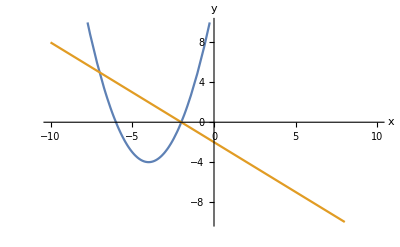

```mathematica
slika2=Plot[{x^2+8x+12,-x-2},{x,-10,10},PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
Solve[x^2+2x-3==-2x-7]
```

{{x→-2},{x→-2}}

```mathematica
Remove[f,x]
```

```mathematica
f[x_]:=-2x-7;
```

```mathematica
f[-2]
```

-3

V tem primeru sta točki na enakem mestu, kar pomeni da se premica in parabola le dotakneta, P(-2,-3).

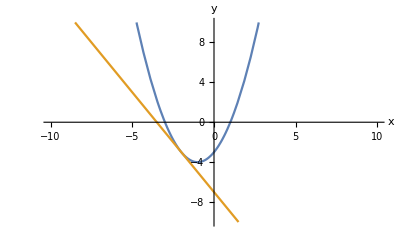

```mathematica
slika3=Plot[{x^2+2x-3,-2x-7},{x,-10,10}, PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
Solve[-x^2+3==x-3]
```

{{x→-3},{x→2}}

```mathematica
Remove[f,x]
```

```mathematica
f[x_]:=x-3;
```

```mathematica
f[-3]
```

-6

```mathematica
f[2]
```

-1

P1(-3,-6), P2(2,-1).

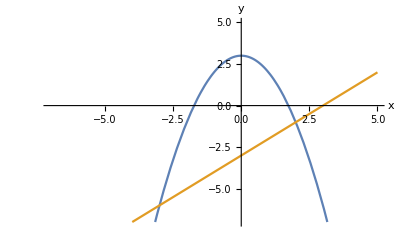

```mathematica
slika4=Plot[{-x^2+3,x-3},{x,-7,5}, PlotRange->{-7,5}, AxesLabel->{"x","y"}]
```

## 6. Reši enačbo:

```mathematica
Solve[Log[x-2,7x-8]==3]
```

{{x→5}}

```mathematica
Solve[Log[3-4x,2x-1]==2]
```

{{x→5/8}}

```mathematica
Solve[2*Log[10,√(x-9)]+Log[10,2x-1]==2]
```

{{x→13}}

```mathematica
Solve[Log[x-1,2x+1]+Log[x-1,x-3]==2]
```

{{x→-1},{x→4}}

V tem primeru je rešitev x=-1 neveljavna, saj mora biti osnova logaritma pozitivno realno število.

```mathematica
Solve[Log[5,x^2-7x-5]==2]
```

{{x→-3},{x→10}}

```mathematica
Solve[Log[√3,2 x^2-x]==2]
```

{{x→-1},{x→3/2}}

## 7. Nariši graf racionalne funkcije:

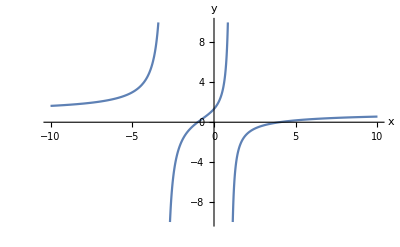

```mathematica
Plot[{(x^2-3 x-4)/(x^2+2 x-3)},{x,-10,10},PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

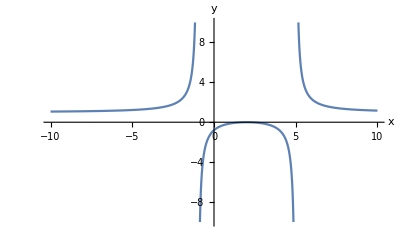

```mathematica
Plot[(x^2-4 x+4)/(x^2-4 x-5),{x,-10,10},PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

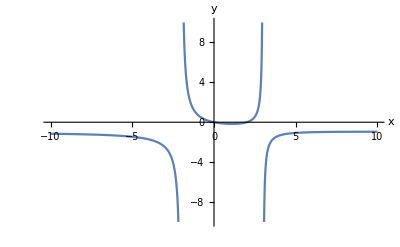

```mathematica
Plot[(x^2-2 x)/(-x^2+ x+6),{x,-10,10},PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

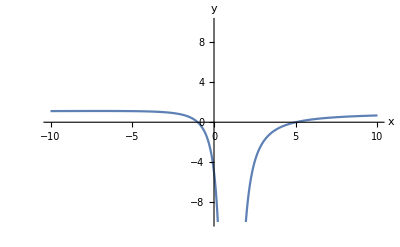

```mathematica
Plot[(x^2-4 x-5)/(x^2-2 x+1),{x,-10,10},PlotRange->{-10,10}, AxesLabel->{"x","y"}]
```

## 8. Poišči vrednosti kotnih funkcij in poenostavi izraz:

```mathematica
FullSimplify[(Sin[2115 Degree]-Cos[(19π)/6])/(Cot[780 Degree]+Sin[-150 Degree])]
```

(-√2+√3) (3+2 √3)

```mathematica
FullSimplify[(Cos[330 Degree]-Sin[1470 Degree])/(Cot[60 Degree]+Tan[-225 Degree])]
```

-(√3)/2

```mathematica
FullSimplify[(Sin[1110 Degree]+Cos[(5π)/6])/(Cos[-330 Degree]-Tan[225 Degree])]
```

1+√3

```mathematica
FullSimplify[(Tan[210 Degree]+Sin[1530 Degree])/(Cos[π/6]-Sin[-90 Degree])]
```

2-2/(√3)

## 9. Določi naklonski kot tangent na funkcijo f(x)=2*sin-√3 v njenih ničlah.

```mathematica
Remove[f,x]
```

```mathematica
funkcija[x_]:=(2*Sin[x]-√3);
```

```mathematica
graf1=Plot[funkcija[x],{x,0,2Pi}];
```

```mathematica
Odvod[x_]:=D[funkcija[x],x]
```

```mathematica
graf2=Plot[tangenta[x],{x,0,2Pi}];
```

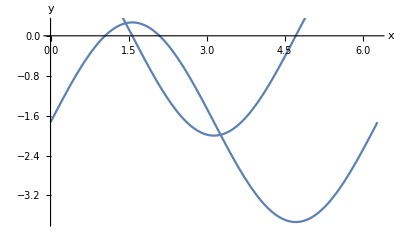

```mathematica
Show[graf1,graf2, AxesLabel->{"x","y"}]
```

Da pridobimo ničle v funkciji, funkcijo enačimo z 0.

```mathematica
Solve[funkcija[x]==0]
```

{{x→ConditionalExpression[π/3+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ]}}

```mathematica
TrigReduce[funkcija[x]==0]
```

-√3+2 Sin[x]==0

Pri tem dobimo, da je sin(x)=(√3)/2, kar je π/3. Vendar ne smemo pozabiti da ima tudi (2 π)/3 enako vrednost pri sinusu.
Da določimo naklonski kot funkcije, naredimo njen odvod.

```mathematica
Odvod[x]
```

2 Cos[x]

Da dobimo naklon tangente funkcije, vnesemo ničle v odvod.

```mathematica
tangenta1a=Odvod[π/3]
```

```mathematica
tangenta1b=Odvod[(2π)/3]
```

Tako dobimo, da je tangenta1a=1, tangenta1b=-1.

Za izračun kota uporabimo tangens. S tem izračunamo naklonski kot tangenta na funkcijo: tangenta1a ima 45 stopinj, tangenta1b pa 135.

## 10. Določi spodnjo in zgornjo mejo zaporedja s splošnim členom a_n=(3n-2)/(6n+4), nato pa za zgornjo mejo svojo trditev še dokaži.

```mathematica
Table[(3x-2)/(6x+4),{x,1,10}]
```

{1/10,1/4,7/22,5/14,13/34,2/5,19/46,11/26,25/58,7/16}

```mathematica
Limit[(3x-2)/(6x+4),x-> Infinity]
```

1/2

```mathematica
Limit[(3x-2)/(6x+4),x-> -Infinity]
```

1/2

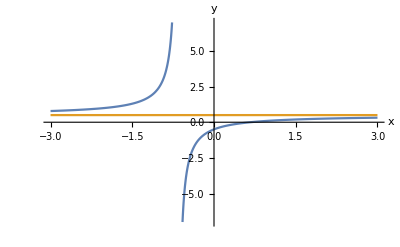

```mathematica
Plot[{(3x-2)/(6x+4),y=1/2},{x,-3,3},PlotRange->{-7,7},AxesLabel->{"x","y"}]
```

Opazimo, da je spodnja in zgornja meja 1/2.

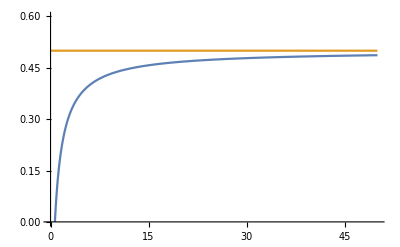

```mathematica
Plot[{(3x-2)/(6x+4), y=1/2},{x,0,50},PlotStyle->{Automatic},PlotRange->{0,0.6}]
```

Da dokažemo zgornjo mejo uporabimo matematično indukcijo, s katero predpostavimo, da je v zaporedju 1. člen manjši od 1/2in nakažemo, da enako velja za slednje.

```mathematica
Remove[f,x]
```

```mathematica
f[x_]:=(3x-2)/(6x+4)<1/2
```

Predpostavimo, da je x=1.

```mathematica
f[1]
```

True

Naredimo preizkus za naslednje člene zaporedja x=x+1.

```mathematica
Simplify[(3(x+1)-2)/(6(x+1)+4)]
```

(1+3 x)/(10+6 x)

```mathematica
f1[x_]:=(1+3 x)/(10+6 x) < 1/2
```

```mathematica
f1[1]
```

True

Ugotovilo smo, da je naslednji člen enako manjši od 1/2, kar nam pove, da je izjava resnična. S tem lahko predpostavimo, da:

V x=1; -1/2≺1/2 in
v x=x+1; 1/10≺1/2.

Če je 1/10 manjša od 1/2, mora biti -1/2 zagotovo manjša od 1/2.


Avtor: Peter Rotar